```mathematica
(*the Franck Condond factors*)
Clear[f, WaveFun];
WaveFun[x_, n_] := 1/Sqrt[2^n n!] Pi^(-1/4) Exp[-(x^2/2)]HermiteH[n,x];

f[a_,-666] := f[a,0];
f[a_,b_] := f[b,a] /; (b>a)
f[a_,b_] := Module[{integral},
integral=
Integrate[WaveFun[x,a] WaveFun[x+Sqrt[2]λ ,b],{x,-Infinity, Infinity}];
f[a,b] := integral ;
integral
]
(*the normal MLJ expression from the vibrational ground state*)
tollMLJ=10^-3;
Clear[TermMLJ, SumMLJ,TermMLJe, SumMLJe];
TermMLJ[S_,hω_, dE_, λi_,kT_,n_]:= S^n/(n!)Exp[-(dE+λi+n hω)^2/(4 λi kT)] Exp[-S]
SumMLJ[S_,hω_, dE_, λi_,kT_]:= SumMLJ[S,hω, dE, λi,kT,0,TermMLJ[S,hω, dE, λi,kT,0],1]
SumMLJ[S_,hω_, dE_, λi_,kT_, valsofar_,dv_,n_] := {valsofar+dv,n} /; (dv/(valsofar+dv) < tollMLJ && n > -Ceiling[dE/hω])
SumMLJ[S_,hω_, dE_, λi_,kT_, valsofar_,dv_,n_] := SumMLJ[S,hω, dE, λi,kT, valsofar+dv,TermMLJ[S,hω, dE, λi,kT,n],n+1] /; (dv/(valsofar+dv) ≥  tollMLJ  || n > -Ceiling[dE/hω])
ΓMLJ[pref_, λi_,hω_, S_, dE_,kT_] :=Module[{exp} ,
exp =  SumMLJ[S, hω, dE,λi,kT];
pref*exp
]
(*the semi classical expression*)
Msm[J_, λ_, ΔG_, kT_]:=J^2/hbar √(Pi/(λ kT)) Exp[-(λ +ΔG)^2/(4 λ kT)]
(*the "normal" MLJ expression from the vibrational excited state i*)
TermMLJe[S_,hω_, dE_, λi_,kT_,{i_,n_}]:= ((f[i,n])/.(λ-> √S ))^2 Exp[-(dE+λi+(n-i) hω)^2/(4 λi kT)]

SumMLJe[S_,hω_, dE_, λi_,kT_, i_]:= SumMLJe[S,hω, dE, λi,kT,i,0.,TermMLJe[S,hω, dE, λi,kT,{i,0}],1]

SumMLJe[S_,hω_, dE_, λi_,kT_, i_ ,valsofar_,dv_,n_] := valsofar+dv /; (dv/(valsofar+dv) < tollMLJ  && n> i)

SumMLJe[S_,hω_, dE_, λi_,kT_, i_ ,valsofar_,dv_,n_] := SumMLJe[S,hω, dE, λi,kT, i, valsofar+dv,TermMLJe[S,hω, dE, λi,kT,{i,n}],n+1] /; (dv/(valsofar+dv) ≥  tollMLJ || n ≤  i)

ΓMLJe[pref_, λi_,hω_, S_, dE_,kT_,i_] :=Module[{exp} ,
exp =  SumMLJ[S, hω, dE,λi,kT];
pref*exp
]
hbar = 6.57 10^-16 (*in eV s^-1*)
Prefactor[J_, λi_,kT_]:= J^2/hbar √(Pi/(λi kT))

P[{A_,S_},{μ_,ν_}]:= 2^(-(μ+ν))KroneckerDelta[A+S, μ+ν]( Sum[Binomial[μ,m] Binomial[ν,n] (-1)^(ν-n)√(((m+n)!(μ+ν-m-n)!)/(μ!ν!))KroneckerDelta[S, m+n],{m,0,μ}, {n,0,ν}])^2
P[{A_,S_}] := P[{A,S},{#,A+S-#}]&/@Range[0, A+S]
```

6.57×10^-16

```mathematica
Clear [GetProbs];
GetProbs[S_, ℏω_, ΔG_,λo_, kT_, nmax_] := GetProbs[S, ℏω, ΔG,λo, kT, nmax,{ϵ-> 4, d-> 10, F-> 0.005}] 

GetProbs[S_, ℏω_, ΔG_,λo_, kT_, nmax_, NRGOptions_]:=Module[{AllΓ,ΔGCorr},
ΔGCorr = ΔG - (27.21 *0.529)/(ϵ d)- F d /. NRGOptions;
AllΓ = TermMLJ[S,ℏω,ΔGCorr, λo,kT,#]&/@ Range[0,nmax];
{SymmProb-> AllΓ/Total[AllΓ],LocalisedProbs->  Total[(AllΓ/Total[AllΓ])⟦#⟧ PadRight[P[{0,#}],nmax+1] &/@ Range[1,nmax+1]]}]
```

Let us use the yields from theone  ϵ model with field 0.005/A, σ=0 d=5nm

```mathematica
range=-1.0 + (0.8 Range[1,100])/100;
```

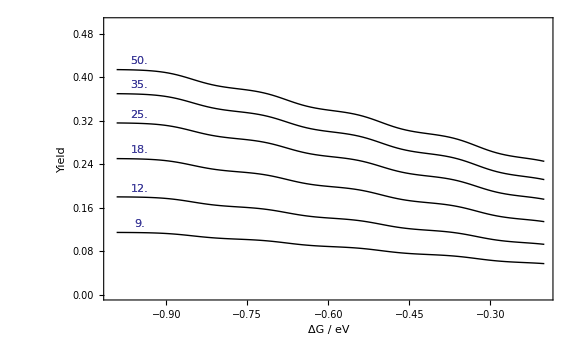

Jdep.eps

```mathematica
PlotYJ[yields_] := Show[ListLinePlot[{{#,Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,7] )*Delete[yields,1]]}&/@ range},  PlotStyle -> {Black,Thick}, PlotRange-> {{-1.,-.2}, {0, 0.5}}] ,
ListPlot[{{-0.95, 0.015+ Total[(LocalisedProbs/. GetProbs[1, 0.17,-1.5,0.1, 0.025,7] )*Delete[yields,1]]}}, PlotMarkers -> Text[Style[ToString[10^3 Round[yields⟦1⟧,0.001]],Black, FontSize-> 16]], PlotRange-> {{-1.,-.2}, {0, 0.5}}]]
allJ = Import["/home/james/Documents/Andrew_Andrew/MCExc/eps4F5/Jsmall/series/RES", "Table"];
plotyj= Show[PlotYJ[#] &/@ allJ, ImageSize-> Large, Frame-> True,  FrameLabel-> {"ΔG / eV", "Yield"}, LabelStyle-> Large]
Export["Jdep.eps",%]
```

0.114435

0.179965

0.250467

0.316169

0.370106

0.414446

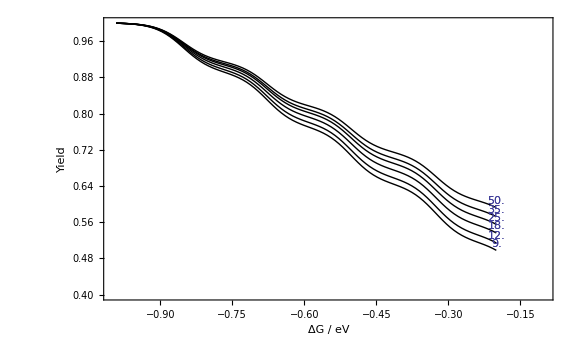

JdepNorm.eps

```mathematica
PlotYJNorm[yields_] := Module[{normal},
normal = Total[(LocalisedProbs/. GetProbs[1, 0.17,range⟦1⟧,0.1, 0.025,7] )*Delete[yields,1]] ;
Print[normal];
Show[ListLinePlot[{{#,Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,7] )*Delete[yields,1]]/normal}&/@ range},  PlotStyle -> {Black,Thick}, PlotRange-> {{-1.,-.1}, {0.4,1}}] ,
ListPlot[{{-0.2, 0.015+ Total[(LocalisedProbs/. GetProbs[1, 0.17,-0.2,0.1, 0.025,7] )*Delete[yields,1]]/normal}}, PlotMarkers -> Text[Style[ToString[10^3 Round[yields⟦1⟧,0.001]],Black, FontSize-> 16]], PlotRange-> {{-1.,-.1}, {0.4,1}}]]
]
plotyjN= Show[PlotYJNorm[#] &/@ allJ, ImageSize-> Large, Frame-> True,  FrameLabel-> {"ΔG / eV", "Yield"}, LabelStyle-> Large]
Export["JdepNorm.eps",%]
```

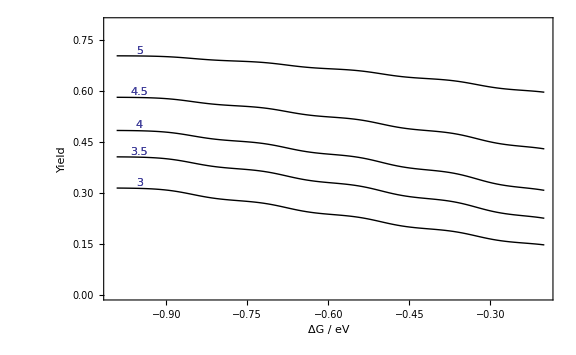

Jeps.eps

```mathematica
PlotYϵ[yields_] := Show[ListLinePlot[{{#,Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,7] )*Delete[yields,1]]}&/@ range},  PlotStyle -> {Black,Thick}, PlotRange-> {{-1.,-.2}, {0, 0.8}}] ,
ListPlot[{{-0.95, 0.015+ Total[(LocalisedProbs/. GetProbs[1, 0.17,-1.5,0.1, 0.025,7] )*Delete[yields,1]]}}, PlotMarkers -> Text[Style[ToString[yields⟦1⟧],Black, FontSize-> 16]], PlotRange-> {{-1.,-.2}, {0, 0.8}}]]
allϵ = Import["/home/james/Documents/Andrew_Andrew/MCExc/eps4F5/eps/series/RES", "Table"];
plotyϵ= Show[PlotYϵ[#] &/@ allϵ, ImageSize-> Large, Frame-> True,  FrameLabel-> {"ΔG / eV", "Yield"}, LabelStyle-> Large]
Export["Jeps.eps",%]
```

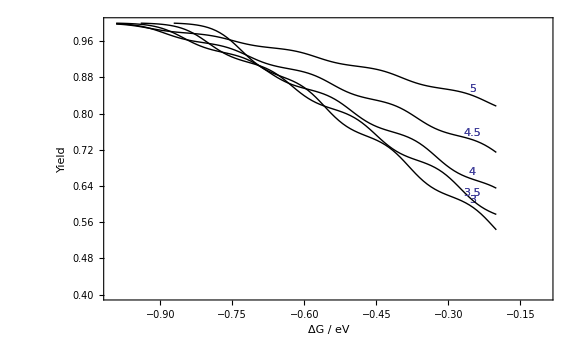

JepsNorm.eps

```mathematica
PlotYϵNorm[yields_] := Module[{normal},
normal=Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,7] )*Delete[yields,1]]&[range⟦1⟧]; Show[ListLinePlot[{{#,Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,7,{ϵ-> yields⟦1⟧, F-> 0.005, d->10}] )*Delete[yields,1]]/normal}&/@ range},  PlotStyle -> {Black,Thick}, PlotRange-> {{-1.,-.1}, {0.4,1}}] ,
ListPlot[{{-0.25, 0.015+ Total[(LocalisedProbs/. GetProbs[1, 0.17,-.25,0.1, 0.025,7,{ϵ-> yields⟦1⟧, F-> 0.005, d->10}] )*Delete[yields,1]]/normal}}, PlotMarkers -> Text[Style[ToString[yields⟦1⟧],Black, FontSize-> 16]], PlotRange-> {{-1.,-.1}, {0.4, 1}}]]
]
allϵ = Import["/home/james/Documents/Andrew_Andrew/MCExc/eps4F5/eps/series/RES", "Table"];
plotyϵN= Show[PlotYϵNorm[#] &/@ allϵ, ImageSize-> Large, Frame-> True,  FrameLabel-> {"ΔG / eV", "Yield"}, LabelStyle-> Large]
Export["JepsNorm.eps",%]
```

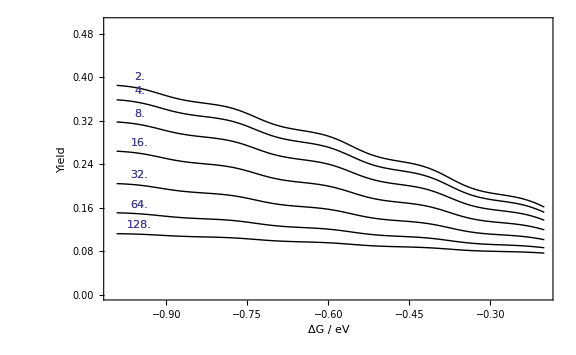

vibdep.eps

```mathematica
PlotYViv[yields_] := Show[ListLinePlot[{{#,Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,5] )*Delete[yields,1]]}&/@ range},  PlotStyle -> {Black,Thick}, PlotRange-> {{-1,-.2}, {0, 0.5}}] ,
ListPlot[{{-.95, 0.015+ Total[(LocalisedProbs/. GetProbs[1, 0.17,-1.,0.1, 0.025,5] )*Delete[yields,1]]}}, PlotMarkers -> Text[Style[ToString[10^-12 yields⟦1⟧],Black, FontSize-> 16]], PlotRange-> {{-1,-.2}, {0, 0.5}}]]

allV = Import["/home/james/Documents/Andrew_Andrew/MCExc/eps4F5/vib14/series/RES", "Table"];
plotyvib = Show[PlotYViv[#] &/@ Delete[allV,1], ImageSize-> Large, Frame-> True,  FrameLabel-> {"ΔG / eV", "Yield"}, LabelStyle-> Large]
Export["vibdep.eps",%]
```

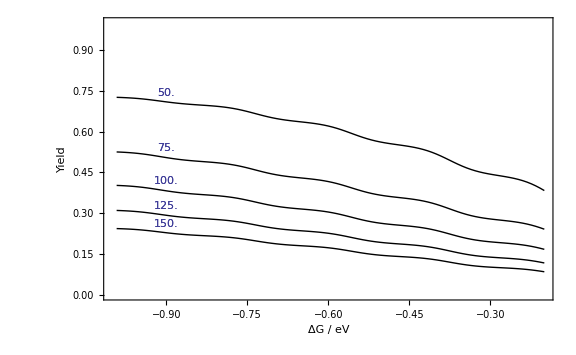

lamouterdep.eps

```mathematica
PlotYLO[yields_] := Show[ListLinePlot[{{#,Total[(LocalisedProbs/. GetProbs[1, 0.17,#,0.1, 0.025,5] )*Delete[yields,1]]}&/@ range},  PlotStyle -> {Black,Thick}, PlotRange-> {{-1,-.2}, {0, 1.0}}] ,
ListPlot[{{-0.9, 0.015+ Total[(LocalisedProbs/. GetProbs[1, 0.17,-1.,0.1, 0.025,5] )*Delete[yields,1]]}}, PlotMarkers -> Text[Style[ToString[10^3 Round[yields⟦1⟧,0.001]],Black, FontSize-> 16]], PlotRange-> {{-1,-.2}, {0, 1.0}}]]

allLO= Import["/home/james/Documents/Andrew_Andrew/MCExc/eps4F5/lobig/series/RES", "Table"];
plotylo= Show[PlotYLO[#] &/@ allLO, ImageSize-> Large, Frame-> True,  FrameLabel-> {"ΔG / eV", "Yield"}, LabelStyle-> Large]
Export["lamouterdep.eps",%]
```

```mathematica
dir = "/home/james/Documents/Andrew_Andrew/MCExc/eps4F5/analyse_res/";
```

```mathematica
Vib12 =Import[dir<>"vib12_condprob.dat", "Table"];
Vib14 =Import[dir<>"vib14_condprob.dat", "Table"];
Jsmall =Import[dir<>"Jsmall_condprob.dat", "Table"];
lobig =Import[dir<>"lobig_condprob.dat", "Table"];
```

```mathematica
GetNthRow[table_, row_]:= {#⟦1⟧,#⟦row⟧} &/@  table
```

```mathematica
GetNthRow[Vib12, 3]
```

{{2,0.933402},{3,0.340508},{4,0.64141},{5,0.883847},{6,0.96998},{7,0.993992}}

```mathematica
PlotNthRow[table_, row_] := Show[ ListLinePlot[GetNthRow[table,row], PlotRange-> {{1.9,7.1},{0,1.1}}, Frame-> True, FrameLabel->  {"d","p(d|d-1)" }, PlotStyle-> {Black,Dashed}], Graphics[Text[ Style[ToString[row-2],FontSize->Large],(GetNthRow[table,row])⟦If[row==2,1,2]⟧+If[row==2,{0,0.05},{(row-2.5)/10,If[row>4,0,0.05]}]]]]
```

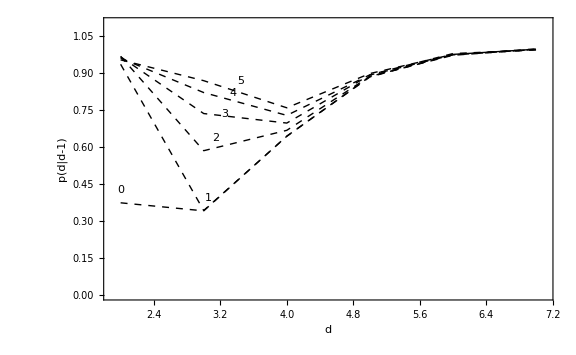

```mathematica
vib12fig = Show[PlotNthRow[Vib12, #] &/@ Range[2,7], LabelStyle-> {FontSize-> Large},ImageSize-> Large]
Jsmallfig = Show[PlotNthRow[Jsmall,#] &/@ Range[2,7], LabelStyle-> {FontSize-> Large}, ImageSize-> Large];
vib14fig = Show[PlotNthRow[Vib14, #] &/@ Range[2,7], LabelStyle-> {FontSize-> Large}, ImageSize-> Large];
lobigfig =Show[PlotNthRow[lobig, #] &/@ Range[2,7], LabelStyle-> {FontSize-> Large}, ImageSize-> Large];
```

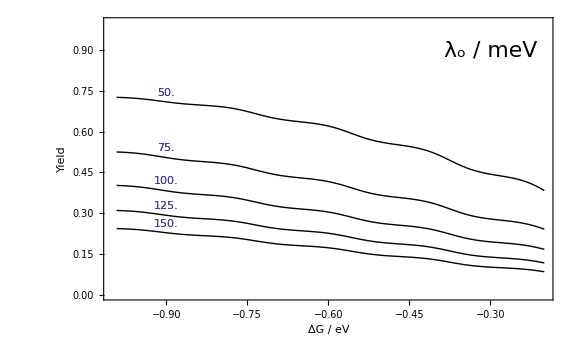

```mathematica
plotylocom= Show[plotylo, Graphics[Text[Style["λ_o / meV", FontSize-> 22], {-0.3,0.9}] ] ]
```

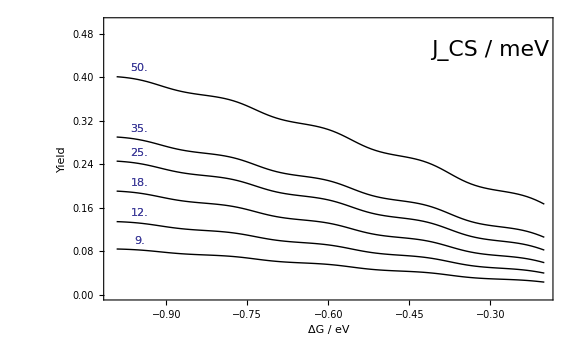

```mathematica
plotyjcom=Show[plotyj, Graphics[Text[Style["J_CS / meV", FontSize-> 22], {-0.3,0.45}] ] ]
```

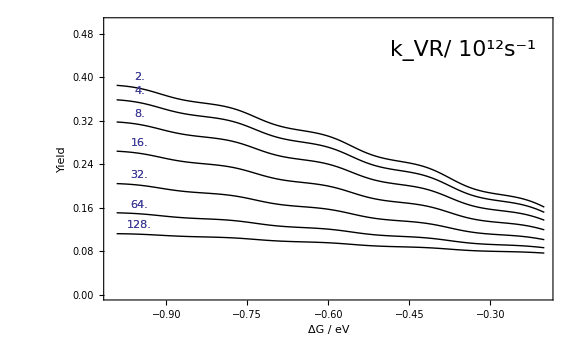

```mathematica
plotyvibcom = Show[plotyvib, Graphics[Text[Style["k_VR/ 10^12s^-1", FontSize-> 22], {-0.35,0.45}] ] ]
```

```mathematica
vib12figcom = Show[vib12fig]
```

-Graphics-

```mathematica
PlotLProb[dg_] := (Interpolation[{#-1,(LocalisedProbs/. GetProbs[1, 0.17,dg,0.1, 0.025,5] )⟦#⟧} &/@ Range[1,6]])[x]
```

```mathematica
UberPlot=Plot3D[PlotLProb[dg], {dg,-1.,-.2} ,{x, 0,5}, Mesh-> {4,0}, PlotStyle-> None]
```

-Graphics3D-

```mathematica
Show[UberPlot, AxesLabel-> {"ΔE/eV", "|ν⟩", "p"}, ImageSize-> Large,LabelStyle-> Large]
```

-Graphics3D-

```mathematica
Export["distribution3d.eps", %]
```

distribution3d.eps

```mathematica
Export["distribution3d.jpeg", %92]
```

distribution3d.jpeg

```mathematica
ProbPlot=PlotLProb[#] &/@ {-1., -.8, -.6,-.4,-.2}
```

{InterpolatingFunction[{{0.,5.}},<>][x],InterpolatingFunction[{{0.,5.}},<>][x],InterpolatingFunction[{{0.,5.}},<>][x],InterpolatingFunction[{{0.,5.}},<>][x],InterpolatingFunction[{{0.,5.}},<>][x]}

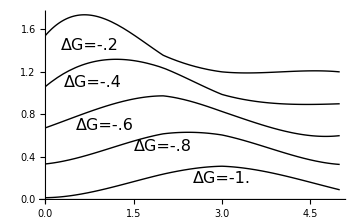

```mathematica
probplot =Show[Plot[ProbPlot⟦#⟧+0.3(#-1) &/@ Range[1,5], {x,0,5}, Axes-> {True, False}, AxesLabel-> {"|ν⟩"}, LabelStyle-> Large, PlotStyle-> {Black, Thick}, ImageSize-> Medium],
Graphics[{Text[Style["ΔG=-1.",FontSize->16],{3,0.2}],Text[Style["ΔG=-.8",FontSize->16],{2,0.5}],Text[Style["ΔG=-.6",FontSize->16],{1,0.7}],Text[Style["ΔG=-.4",FontSize->16],{0.8,1.1}],Text[Style["ΔG=-.2",FontSize->16],{0.75,1.45}]}]]
```

```mathematica
Export["probplot.eps", probplot]
```

probplot.eps

```mathematica
Export["probplot.jpeg",Show[ probplot, ImageSize-> Large]]
```

probplot.jpeg

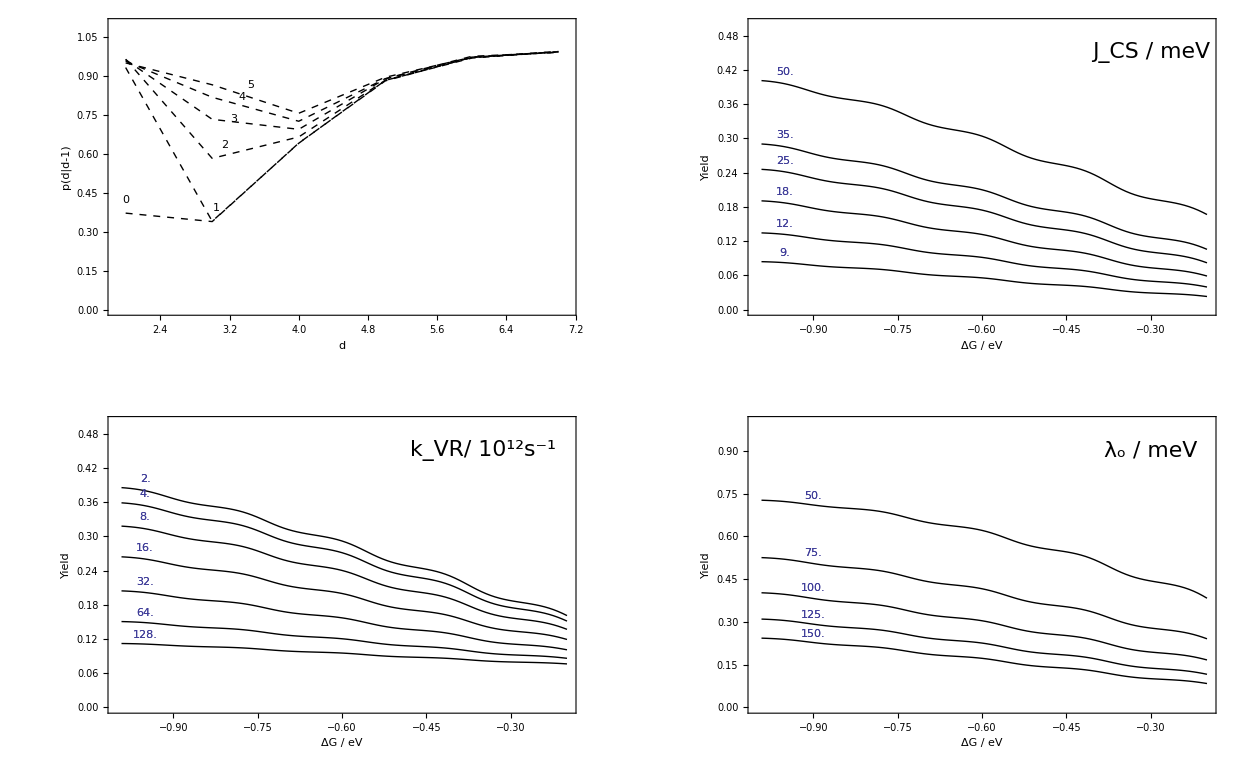

fig2.eps

```mathematica
fig2 = GraphicsGrid[{{ vib12figcom, plotyjcom},{plotyvibcom,plotylocom}}]
Export["fig2.eps", fig2]
```

```mathematica
1.04142 10^11+ 3.18037 10^11
```

4.22179×10^11